```mathematica
x=.; Remove["Global`*"];
Off[General::spell1];
ClearAll
```

ClearAll

```mathematica
conjugateRule={Complex[re_,im_]:>Complex[re,-im]};
conjugate[z_]:=z/.conjugateRule;
real[z_]:=(1/2)*(z+conjugate[z])//Simplify;
imag[z_]:=(-I/2)*(z-conjugate[z])//Simplify;
abs[z_]:=Sqrt[(z*(z/.conjugateRule))]//Simplify;
```

```mathematica
(*SetDirectory["D:\\Cuba\\Cuba-4.2"]
Install["Vegas"];
Install["Divonne"];
Install["Suave"];
Install["Cuhre"];
```

## Constants

```mathematica
c=299792458 ;hb=1.0545715964207855*10^-34;q=1.602*10^-19;ϵ0=8.85*10^-12;m=9.1*10^-31;a0=3.5668*10^-10;den=8/a0^3;den1=2/a0^3;G=Sqrt[2^2+2^2+0^2]*2*Pi/a0;normstructurefactor=8/8;atomscatfactor=1.603;re=2.82*10^-13*10^-2;ϵ0=8.85*10^-12;m=9.1*10^-31;
```

```mathematica
λv[w_]:=2*Pi*c/w*10^9
```

```mathematica
Plot[λv[w],{w,2*Pi*c/2000*10^9,2*Pi*c/200*10^9}]
```

-Graphics-

## Scattering Factors (Carbon)

Note : Carbon data are hidden in the following cell.

```mathematica
carbondata={{29.3,4.451*^16,3.6332,2.7402,"","","","","","",""},{29.774,4.523*^16,3.6738,2.6898,"","","","","","",""},{30.256,4.5961*^16,3.7127,2.6362,"","","","","","",""},{30.745,4.6705*^16,3.7475,2.5836,"","","","","","",""},{31.242,4.746*^16,3.7797,2.5321,"","","","","","",""},{31.747,4.8228*^16,3.8097,2.4815,"","","","","","",""},{32.261,4.9008*^16,3.8376,2.432,"","","","","","",""},{32.783,4.98*^16,3.8637,2.3835,"","","","","","",""},{33.313,5.0606*^16,3.8881,2.336,"","","","","","",""},{33.852,5.1424*^16,3.9107,2.2894,"","","","","","",""},{34.399,5.2256*^16,3.9316,2.2437,"","","","","","",""},{34.956,5.3101*^16,3.9503,2.199,"","","","","","",""},{35.521,5.396*^16,3.9671,2.158,"","","","","","",""},{36.096,5.4833*^16,3.9849,2.1183,"","","","","","",""},{36.679,5.572*^16,4.0025,2.0793,"","","","","","",""},{37.273,5.6621*^16,4.0199,2.041,"","","","","","",""},{37.875,5.7537*^16,4.0371,2.0034,"","","","","","",""},{38.488,5.8467*^16,4.0543,1.9666,"","","","","","",""},{39.111,5.9413*^16,4.0736,1.9304,"","","","","","",""},{39.743,6.0374*^16,4.0945,1.8901,"","","","","","",""},{40.386,6.1351*^16,4.1101,1.8465,"","","","","","",""},{41.039,6.2343*^16,4.1223,1.8039,"","","","","","",""},{41.703,6.3351*^16,4.1321,1.7623,"","","","","","",""},{42.378,6.4376*^16,4.1399,1.7216,"","","","","","",""},{43.063,6.5417*^16,4.1456,1.6819,"","","","","","",""},{43.759,6.6475*^16,4.1493,1.6431,"","","","","","",""},{44.467,6.755*^16,4.1495,1.6052,"","","","","","",""},{45.187,6.8643*^16,4.1458,1.5692,"","","","","","",""},{45.917,6.9753*^16,4.1417,1.5438,"","","","","","",""},{46.66,7.0881*^16,4.1417,1.5188,"","","","","","",""},{47.415,7.2028*^16,4.143,1.4942,"","","","","","",""},{48.182,7.3193*^16,4.1449,1.47,"","","","","","",""},{48.961,7.4377*^16,4.147,1.4462,"","","","","","",""},{49.753,7.5579*^16,4.1491,1.4228,"","","","","","",""},{50.558,7.6802*^16,4.1511,1.3997,"","","","","","",""},{51.375,7.8044*^16,4.1528,1.3771,"","","","","","",""},{52.206,7.9306*^16,4.1537,1.3548,"","","","","","",""},{53.051,8.0589*^16,4.1531,1.3328,"","","","","","",""},{53.909,8.1893*^16,4.1496,1.3155,"","","","","","",""},{54.781,8.3217*^16,4.15,1.3017,"","","","","","",""},{55.667,8.4563*^16,4.1527,1.288,"","","","","","",""},{56.567,8.5931*^16,4.1568,1.2745,"","","","","","",""},{57.482,8.7321*^16,4.1621,1.2612,"","","","","","",""},{58.412,8.8733*^16,4.1685,1.248,"","","","","","",""},{59.356,9.0168*^16,4.1762,1.2349,"","","","","","",""},{60.317,9.1627*^16,4.186,1.222,"","","","","","",""},{61.292,9.3109*^16,4.1995,1.2065,"","","","","","",""},{62.283,9.4615*^16,4.211,1.185,"","","","","","",""},{63.291,9.6145*^16,4.2191,1.1638,"","","","","","",""},{64.314,9.77*^16,4.2258,1.143,"","","","","","",""},{65.355,9.928*^16,4.2316,1.1226,"","","","","","",""},{66.412,1.0089*^17,4.2367,1.1025,"","","","","","",""},{67.486,1.0252*^17,4.2411,1.0828,"","","","","","",""},{68.577,1.0418*^17,4.245,1.0635,"","","","","","",""},{69.687,1.0586*^17,4.2485,1.0445,"","","","","","",""},{70.814,1.0757*^17,4.2516,1.0258,"","","","","","",""},{71.959,1.0931*^17,4.2543,1.0075,"","","","","","",""},{73.123,1.1108*^17,4.2567,0.98947,"","","","","","",""},{74.306,1.1288*^17,4.2587,0.97179,"","","","","","",""},{75.508,1.147*^17,4.2605,0.95442,"","","","","","",""},{76.729,1.1656*^17,4.2619,0.93737,"","","","","","",""},{77.97,1.1844*^17,4.2631,0.92062,"","","","","","",""},{79.231,1.2036*^17,4.2641,0.90417,"","","","","","",""},{80.512,1.2231*^17,4.2648,0.88801,"","","","","","",""},{81.815,1.2428*^17,4.2652,0.87214,"","","","","","",""},{83.138,1.2629*^17,4.2655,0.85656,"","","","","","",""},{84.483,1.2834*^17,4.2655,0.84125,"","","","","","",""},{85.849,1.3041*^17,4.2653,0.82622,"","","","","","",""},{87.238,1.3252*^17,4.2648,0.81145,"","","","","","",""},{88.649,1.3467*^17,4.2642,0.79695,"","","","","","",""},{90.082,1.3684*^17,4.2633,0.78271,"","","","","","",""},{91.539,1.3906*^17,4.2623,0.76872,"","","","","","",""},{93.02,1.4131*^17,4.261,0.75499,"","","","","","",""},{94.525,1.4359*^17,4.2595,0.7415,"","","","","","",""},{96.053,1.4591*^17,4.2579,0.72825,"","","","","","",""},{97.607,1.4827*^17,4.256,0.71523,"","","","","","",""},{99.186,1.5067*^17,4.2539,0.70245,"","","","","","",""},{100.79,1.5311*^17,4.2517,0.6899,"","","","","","",""},{102.42,1.5559*^17,4.2492,0.67757,"","","","","","",""},{104.08,1.581*^17,4.2465,0.66546,"","","","","","",""},{105.76,1.6066*^17,4.2436,0.65357,"","","","","","",""},{107.47,1.6326*^17,4.2405,0.64189,"","","","","","",""},{109.21,1.659*^17,4.2372,0.63042,"","","","","","",""},{110.97,1.6858*^17,4.2337,0.61916,"","","","","","",""},{112.77,1.7131*^17,4.23,0.60809,"","","","","","",""},{114.59,1.7408*^17,4.2261,0.59722,"","","","","","",""},{116.45,1.769*^17,4.2219,0.58655,"","","","","","",""},{118.33,1.7976*^17,4.2175,0.57607,"","","","","","",""},{120.25,1.8266*^17,4.2129,0.56578,"","","","","","",""},{122.19,1.8562*^17,4.2081,0.55567,"","","","","","",""},{124.17,1.8862*^17,4.203,0.54574,"","","","","","",""},{126.18,1.9167*^17,4.1977,0.53598,"","","","","","",""},{128.21,1.9477*^17,4.1922,0.52641,"","","","","","",""},{130.29,1.9792*^17,4.1867,0.517,"","","","","","",""},{132.4,2.0112*^17,4.1812,0.50776,"","","","","","",""},{134.54,2.0438*^17,4.1753,0.49746,"","","","","","",""},{136.71,2.0768*^17,4.1686,0.48736,"","","","","","",""},{138.93,2.1104*^17,4.1612,0.47747,"","","","","","",""},{141.17,2.1445*^17,4.1533,0.46778,"","","","","","",""},{143.46,2.1792*^17,4.1448,0.45828,"","","","","","",""},{145.78,2.2145*^17,4.1359,0.44898,"","","","","","",""},{148.13,2.2503*^17,4.1264,0.43987,"","","","","","",""},{150.53,2.2867*^17,4.1164,0.43094,"","","","","","",""},{152.96,2.3237*^17,4.1058,0.42219,"","","","","","",""},{155.44,2.3613*^17,4.0946,0.41362,"","","","","","",""},{157.95,2.3995*^17,4.0829,0.40523,"","","","","","",""},{160.51,2.4383*^17,4.0705,0.397,"","","","","","",""},{163.1,2.4777*^17,4.0575,0.38895,"","","","","","",""},{165.74,2.5178*^17,4.0438,0.38105,"","","","","","",""},{168.42,2.5585*^17,4.0294,0.37332,"","","","","","",""},{171.15,2.5999*^17,4.0143,0.36574,"","","","","","",""},{173.91,2.6419*^17,3.9983,0.35832,"","","","","","",""},{176.73,2.6847*^17,3.9816,0.35105,"","","","","","",""},{179.59,2.7281*^17,3.964,0.34392,"","","","","","",""},{182.49,2.7722*^17,3.9456,0.33694,"","","","","","",""},{185.44,2.817*^17,3.9272,0.3301,"","","","","","",""},{188.44,2.8626*^17,3.907,0.321,"","","","","","",""},{191.49,2.9089*^17,3.8844,0.3121,"","","","","","",""},{194.59,2.956*^17,3.8598,0.30344,"","","","","","",""},{197.73,3.0038*^17,3.8331,0.29503,"","","","","","",""},{200.93,3.0524*^17,3.8043,0.28685,"","","","","","",""},{204.18,3.1017*^17,3.7732,0.2789,"","","","","","",""},{207.49,3.1519*^17,3.7397,0.27117,"","","","","","",""},{210.84,3.2029*^17,3.7035,0.26365,"","","","","","",""},{214.25,3.2547*^17,3.6643,0.25634,"","","","","","",""},{217.72,3.3073*^17,3.6216,0.24923,"","","","","","",""},{221.24,3.3608*^17,3.575,0.24252,"","","","","","",""},{224.82,3.4152*^17,3.5243,0.23638,"","","","","","",""},{228.45,3.4704*^17,3.469,0.2304,"","","","","","",""},{232.15,3.5265*^17,3.4081,0.22457,"","","","","","",""},{235.9,3.5836*^17,3.3406,0.21889,"","","","","","",""},{239.72,3.6415*^17,3.2652,0.21336,"","","","","","",""},{243.6,3.7005*^17,3.1803,0.20796,"","","","","","",""},{247.54,3.7603*^17,3.0847,0.20218,"","","","","","",""},{251.54,3.8211*^17,2.9729,0.19468,"","","","","","",""},{255.61,3.8829*^17,2.84,0.18746,"","","","","","",""},{259.74,3.9457*^17,2.6799,0.18051,"","","","","","",""},{263.94,4.0095*^17,2.4814,0.17382,"","","","","","",""},{268.21,4.0744*^17,2.225,0.16738,"","","","","","",""},{272.55,4.1403*^17,1.8716,0.16117,"","","","","","",""},{276.96,4.2073*^17,1.3219,0.15519,"","","","","","",""},{281.44,4.2753*^17,0.15857,0.14944,"","","","","","",""},{284.1,4.3158*^17,-4.0488,0.14616,"","","","","","",""},{284.3,4.3188*^17,-4.0403,4.1887,"","","","","","",""},{285.99,4.3445*^17,-0.28333,4.1586,"","","","","","",""},{290.61,4.4147*^17,1.4397,4.078,"","","","","","",""},{295.32,4.4861*^17,2.2058,3.999,"","","","","","",""},{300.09,4.5587*^17,2.7129,3.9215,"","","","","","",""},{304.95,4.6324*^17,3.0947,3.8455,"","","","","","",""},{309.88,4.7074*^17,3.4019,3.771,"","","","","","",""},{314.89,4.7835*^17,3.6588,3.6979,"","","","","","",""},{319.98,4.8609*^17,3.8797,3.6262,"","","","","","",""},{325.16,4.9395*^17,4.0732,3.5559,"","","","","","",""},{330.42,5.0194*^17,4.2451,3.487,"","","","","","",""},{335.76,5.1006*^17,4.3997,3.4195,"","","","","","",""},{341.19,5.183*^17,4.5399,3.3532,"","","","","","",""},{346.71,5.2669*^17,4.6682,3.2882,"","","","","","",""},{352.32,5.3521*^17,4.7864,3.2245,"","","","","","",""},{358.02,5.4386*^17,4.8961,3.162,"","","","","","",""},{363.81,5.5266*^17,4.9985,3.1007,"","","","","","",""},{369.69,5.616*^17,5.0952,3.0406,"","","","","","",""},{375.67,5.7068*^17,5.1891,2.9817,"","","","","","",""},{381.75,5.7991*^17,5.2793,2.9165,"","","","","","",""},{387.92,5.8929*^17,5.3605,2.8482,"","","","","","",""},{394.2,5.9882*^17,5.4327,2.7814,"","","","","","",""},{400.57,6.0851*^17,5.499,2.7163,"","","","","","",""},{407.05,6.1835*^17,5.5601,2.6526,"","","","","","",""},{413.64,6.2835*^17,5.6167,2.5905,"","","","","","",""},{420.33,6.3852*^17,5.6692,2.5298,"","","","","","",""},{427.12,6.4884*^17,5.718,2.4705,"","","","","","",""},{434.03,6.5934*^17,5.7635,2.4127,"","","","","","",""},{441.05,6.7*^17,5.8059,2.3561,"","","","","","",""},{448.19,6.8084*^17,5.8456,2.3009,"","","","","","",""},{455.43,6.9185*^17,5.8826,2.247,"","","","","","",""},{462.8,7.0304*^17,5.9174,2.1944,"","","","","","",""},{470.29,7.1441*^17,5.95,2.143,"","","","","","",""},{477.89,7.2597*^17,5.9807,2.0928,"","","","","","",""},{485.62,7.3771*^17,6.0102,2.0437,"","","","","","",""},{493.48,7.4964*^17,6.0377,1.9942,"","","","","","",""},{501.46,7.6177*^17,6.0627,1.9459,"","","","","","",""},{509.57,7.7409*^17,6.0858,1.8988,"","","","","","",""},{517.81,7.8661*^17,6.1072,1.8528,"","","","","","",""},{526.19,7.9933*^17,6.1271,1.8079,"","","","","","",""},{534.7,8.1226*^17,6.1456,1.7641,"","","","","","",""},{543.35,8.254*^17,6.1627,1.7214,"","","","","","",""},{552.13,8.3875*^17,6.1786,1.6797,"","","","","","",""},{561.07,8.5231*^17,6.1934,1.639,"","","","","","",""},{570.14,8.661*^17,6.2072,1.5993,"","","","","","",""},{579.36,8.8011*^17,6.2199,1.5606,"","","","","","",""},{588.73,8.9434*^17,6.2317,1.5228,"","","","","","",""},{598.25,9.0881*^17,6.2427,1.4859,"","","","","","",""},{607.93,9.2351*^17,6.2529,1.4499,"","","","","","",""},{617.76,9.3844*^17,6.2623,1.4148,"","","","","","",""},{627.76,9.5362*^17,6.271,1.3806,"","","","","","",""},{637.91,9.6905*^17,6.279,1.3471,"","","","","","",""},{648.23,9.8472*^17,6.2864,1.3145,"","","","","","",""},{658.71,1.0006*^18,6.2931,1.2827,"","","","","","",""},{669.36,1.0168*^18,6.299,1.2516,"","","","","","",""},{680.19,1.0333*^18,6.3041,1.2225,"","","","","","",""},{691.19,1.05*^18,6.3097,1.1952,"","","","","","",""},{702.37,1.067*^18,6.3182,1.169,"","","","","","",""},{713.73,1.0842*^18,6.3278,1.1396,"","","","","","",""},{725.28,1.1018*^18,6.3345,1.1084,"","","","","","",""},{737.01,1.1196*^18,6.3393,1.0782,"","","","","","",""},{748.93,1.1377*^18,6.3431,1.0487,"","","","","","",""},{761.04,1.1561*^18,6.3459,1.0201,"","","","","","",""},{773.35,1.1748*^18,6.3481,0.99218,"","","","","","",""},{785.86,1.1938*^18,6.3497,0.96505,"","","","","","",""},{798.57,1.2131*^18,6.3508,0.93863,"","","","","","",""},{811.49,1.2327*^18,6.3514,0.91294,"","","","","","",""},{824.61,1.2527*^18,6.3516,0.88795,"","","","","","",""},{837.95,1.2729*^18,6.3515,0.86366,"","","","","","",""},{851.5,1.2935*^18,6.3511,0.83992,"","","","","","",""},{865.27,1.3144*^18,6.3504,0.81671,"","","","","","",""},{879.27,1.3357*^18,6.3493,0.79404,"","","","","","",""},{893.49,1.3573*^18,6.3479,0.77201,"","","","","","",""},{907.94,1.3793*^18,6.3463,0.75058,"","","","","","",""},{922.63,1.4016*^18,6.3444,0.72976,"","","","","","",""},{937.55,1.4242*^18,6.3424,0.70936,"","","","","","",""},{952.72,1.4473*^18,6.3402,0.6895,"","","","","","",""},{968.12,1.4707*^18,6.3377,0.67018,"","","","","","",""},{983.78,1.4945*^18,6.335,0.65138,"","","","","","",""},{999.7,1.5186*^18,6.3322,0.63312,"","","","","","",""},{1015.9,1.5432*^18,6.3293,0.61538,"","","","","","",""},{1032.3,1.5682*^18,6.3264,0.59819,"","","","","","",""},{1049.,1.5935*^18,6.3236,0.58123,"","","","","","",""},{1066.,1.6193*^18,6.3205,0.56446,"","","","","","",""},{1083.2,1.6455*^18,6.3171,0.5482,"","","","","","",""},{1100.7,1.6721*^18,6.3136,0.53239,"","","","","","",""},{1118.5,1.6991*^18,6.31,0.51702,"","","","","","",""},{1136.6,1.7266*^18,6.3062,0.50212,"","","","","","",""},{1155.,1.7546*^18,6.3024,0.48764,"","","","","","",""},{1173.7,1.7829*^18,6.2986,0.47358,"","","","","","",""},{1192.7,1.8118*^18,6.2947,0.45993,"","","","","","",""},{1211.9,1.8411*^18,6.2908,0.44668,"","","","","","",""},{1231.6,1.8708*^18,6.2869,0.43379,"","","","","","",""},{1251.5,1.9011*^18,6.2831,0.42118,"","","","","","",""},{1271.7,1.9319*^18,6.2793,0.4088,"","","","","","",""},{1292.3,1.9631*^18,6.2753,0.39665,"","","","","","",""},{1313.2,1.9949*^18,6.2713,0.38487,"","","","","","",""},{1334.4,2.0271*^18,6.2672,0.37344,"","","","","","",""},{1356.,2.0599*^18,6.263,0.36234,"","","","","","",""},{1377.9,2.0932*^18,6.2589,0.35158,"","","","","","",""},{1400.2,2.1271*^18,6.2547,0.34113,"","","","","","",""},{1422.9,2.1615*^18,6.2505,0.33099,"","","","","","",""},{1445.9,2.1965*^18,6.2464,0.32116,"","","","","","",""},{1469.3,2.232*^18,6.2423,0.31161,"","","","","","",""},{1493.,2.2681*^18,6.2382,0.30232,"","","","","","",""},{1517.2,2.3048*^18,6.2342,0.29323,"","","","","","",""},{1541.7,2.342*^18,6.2301,0.28441,"","","","","","",""},{1566.7,2.3799*^18,6.226,0.27585,"","","","","","",""},{1592.,2.4184*^18,6.222,0.26755,"","","","","","",""},{1617.8,2.4575*^18,6.218,0.25949,"","","","","","",""},{1643.9,2.4973*^18,6.214,0.25168,"","","","","","",""},{1670.5,2.5377*^18,6.2101,0.24411,"","","","","","",""},{1697.5,2.5787*^18,6.2062,0.23676,"","","","","","",""},{1725.,2.6204*^18,6.2023,0.22964,"","","","","","",""},{1752.9,2.6628*^18,6.1986,0.22266,"","","","","","",""},{1781.2,2.7059*^18,6.1948,0.21588,"","","","","","",""},{1810.1,2.7496*^18,6.1911,0.20928,"","","","","","",""},{1839.3,2.7941*^18,6.1873,0.20288,"","","","","","",""},{1869.1,2.8393*^18,6.1837,0.19669,"","","","","","",""},{1899.3,2.8852*^18,6.18,0.19068,"","","","","","",""},{1930.,2.9319*^18,6.1764,0.18485,"","","","","","",""},{1961.2,2.9793*^18,6.1729,0.1792,"","","","","","",""},{1993.,3.0275*^18,6.1694,0.17373,"","","","","","",""},{2025.2,3.0765*^18,6.1659,0.16847,"","","","","","",""},{2057.9,3.1262*^18,6.1626,0.16329,"","","","","","",""},{2091.2,3.1768*^18,6.1593,0.15826,"","","","","","",""},{2125.1,3.2282*^18,6.156,0.15338,"","","","","","",""},{2159.4,3.2804*^18,6.1528,0.14865,"","","","","","",""},{2194.4,3.3335*^18,6.1496,0.14405,"","","","","","",""},{2229.9,3.3874*^18,6.1464,0.13959,"","","","","","",""},{2265.9,3.4422*^18,6.1433,0.13527,"","","","","","",""},{2302.6,3.4978*^18,6.1403,0.13107,"","","","","","",""},{2339.8,3.5544*^18,6.1373,0.127,"","","","","","",""},{2377.7,3.6119*^18,6.1343,0.12304,"","","","","","",""},{2416.1,3.6703*^18,6.1314,0.11921,"","","","","","",""},{2455.2,3.7297*^18,6.1286,0.11549,"","","","","","",""},{2494.9,3.79*^18,6.1258,0.11188,"","","","","","",""},{2535.3,3.8513*^18,6.123,0.10838,"","","","","","",""},{2576.3,3.9136*^18,6.1203,0.10499,"","","","","","",""},{2617.9,3.9769*^18,6.1176,0.10169,"","","","","","",""},{2660.3,4.0412*^18,6.115,0.098504,"","","","","","",""},{2703.3,4.1066*^18,6.1124,0.095403,"","","","","","",""},{2747.,4.173*^18,6.1099,0.092397,"","","","","","",""},{2791.5,4.2405*^18,6.1074,0.089483,"","","","","","",""},{2836.6,4.3091*^18,6.105,0.086662,"","","","","","",""},{2882.5,4.3788*^18,6.1026,0.083915,"","","","","","",""},{2929.1,4.4496*^18,6.1002,0.08126,"","","","","","",""},{2976.5,4.5216*^18,6.0979,0.078682,"","","","","","",""},{3024.6,4.5947*^18,6.0957,0.076182,"","","","","","",""},{3073.6,4.669*^18,6.0935,0.073758,"","","","","","",""},{3123.3,4.7445*^18,6.0913,0.071408,"","","","","","",""},{3173.8,4.8213*^18,6.0892,0.069129,"","","","","","",""},{3225.1,4.8993*^18,6.0871,0.066919,"","","","","","",""},{3277.3,4.9785*^18,6.085,0.064777,"","","","","","",""},{3330.3,5.059*^18,6.083,0.062699,"","","","","","",""},{3384.1,5.1409*^18,6.081,0.060685,"","","","","","",""},{3438.9,5.224*^18,6.0791,0.058733,"","","","","","",""},{3494.5,5.3085*^18,6.0772,0.05684,"","","","","","",""},{3551.,5.3944*^18,6.0754,0.055004,"","","","","","",""},{3608.5,5.4816*^18,6.0736,0.053224,"","","","","","",""},{3666.8,5.5703*^18,6.0718,0.0515,"","","","","","",""},{3726.1,5.6604*^18,6.07,0.049828,"","","","","","",""},{3786.4,5.7519*^18,6.0683,0.048207,"","","","","","",""},{3847.6,5.845*^18,6.0667,0.046635,"","","","","","",""},{3909.9,5.9395*^18,6.065,0.045113,"","","","","","",""},{3973.1,6.0356*^18,6.0634,0.043637,"","","","","","",""},{4037.4,6.1332*^18,6.0619,0.042221,"","","","","","",""},{4102.7,6.2324*^18,6.0603,0.040835,"","","","","","",""},{4169.,6.3332*^18,6.0588,0.039492,"","","","","","",""},{4236.5,6.4356*^18,6.0574,0.038192,"","","","","","",""},{4305.,6.5397*^18,6.0559,0.036932,"","","","","","",""},{4374.6,6.6455*^18,6.0545,0.035713,"","","","","","",""},{4445.4,6.753*^18,6.0531,0.034533,"","","","","","",""},{4517.3,6.8622*^18,6.0518,0.03339,"","","","","","",""},{4590.3,6.9732*^18,6.0505,0.032283,"","","","","","",""},{4664.6,7.086*^18,6.0492,0.03121,"","","","","","",""},{4740.,7.2006*^18,6.0479,0.030172,"","","","","","",""},{4816.7,7.317*^18,6.0467,0.029168,"","","","","","",""},{4894.6,7.4354*^18,6.0455,0.028195,"","","","","","",""},{4973.8,7.5557*^18,6.0443,0.027254,"","","","","","",""},{5054.2,7.6779*^18,6.0431,0.026343,"","","","","","",""},{5136.,7.802*^18,6.042,0.025461,"","","","","","",""},{5219.,7.9282*^18,6.0409,0.024607,"","","","","","",""},{5303.4,8.0565*^18,6.0398,0.023781,"","","","","","",""},{5389.2,8.1868*^18,6.0388,0.022981,"","","","","","",""},{5476.4,8.3192*^18,6.0377,0.022206,"","","","","","",""},{5565.,8.4537*^18,6.0367,0.021457,"","","","","","",""},{5655.,8.5905*^18,6.0358,0.020733,"","","","","","",""},{5746.4,8.7294*^18,6.0348,0.020031,"","","","","","",""},{5839.4,8.8706*^18,6.0339,0.019352,"","","","","","",""},{5933.8,9.0141*^18,6.0329,0.018695,"","","","","","",""},{6029.8,9.1599*^18,6.0321,0.018059,"","","","","","",""},{6127.3,9.308*^18,6.0312,0.017445,"","","","","","",""},{6226.4,9.4586*^18,6.0303,0.01685,"","","","","","",""},{6327.1,9.6116*^18,6.0295,0.016275,"","","","","","",""},{6429.5,9.767*^18,6.0287,0.015718,"","","","","","",""},{6533.5,9.925*^18,6.0279,0.015179,"","","","","","",""},{6639.1,1.0086*^19,6.0271,0.014659,"","","","","","",""},{6746.5,1.0249*^19,6.0264,0.014155,"","","","","","",""},{6855.6,1.0414*^19,6.0256,0.013668,"","","","","","",""},{6966.5,1.0583*^19,6.0249,0.013197,"","","","","","",""},{7079.2,1.0754*^19,6.0242,0.012741,"","","","","","",""},{7193.7,1.0928*^19,6.0235,0.0123,"","","","","","",""},{7310.1,1.1105*^19,6.0229,0.011874,"","","","","","",""},{7428.3,1.1284*^19,6.0222,0.011462,"","","","","","",""},{7548.5,1.1467*^19,6.0216,0.011063,"","","","","","",""},{7670.5,1.1652*^19,6.0209,0.010678,"","","","","","",""},{7794.6,1.1841*^19,6.0203,0.010306,"","","","","","",""},{7920.7,1.2032*^19,6.0198,0.0099458,"","","","","","",""},{8048.8,1.2227*^19,6.0192,0.0095978,"","","","","","",""},{8179.,1.2425*^19,6.0186,0.0092613,"","","","","","",""},{8311.3,1.2626*^19,6.0181,0.0089362,"","","","","","",""},{8445.7,1.283*^19,6.0175,0.0086219,"","","","","","",""},{8582.3,1.3037*^19,6.017,0.0083182,"","","","","","",""},{8721.1,1.3248*^19,6.0165,0.0080248,"","","","","","",""},{8862.2,1.3463*^19,6.016,0.007741,"","","","","","",""},{9005.5,1.368*^19,6.0155,0.0074669,"","","","","","",""},{9151.2,1.3902*^19,6.015,0.007202,"","","","","","",""},{9299.2,1.4126*^19,6.0146,0.0069461,"","","","","","",""},{9449.6,1.4355*^19,6.0141,0.006699,"","","","","","",""},{9602.4,1.4587*^19,6.0137,0.0064603,"","","","","","",""},{9757.7,1.4823*^19,6.0133,0.0062294,"","","","","","",""},{9915.5,1.5063*^19,6.0129,0.0060066,"","","","","","",""},{10076,1.5306*^19,6.0125,0.0057914,"","","","","","",""},{10239,1.5554*^19,6.0121,0.0055835,"","","","","","",""},{10405,1.5805*^19,6.0117,0.0053828,"","","","","","",""},{10573,1.6061*^19,6.0113,0.0051889,"","","","","","",""},{10744,1.6321*^19,6.0109,0.0050017,"","","","","","",""},{10918,1.6585*^19,6.0106,0.004821,"","","","","","",""},{11094,1.6853*^19,6.0102,0.0046465,"","","","","","",""},{11274,1.7126*^19,6.0099,0.0044781,"","","","","","",""},{11456,1.7403*^19,6.0096,0.0043155,"","","","","","",""},{11641,1.7684*^19,6.0093,0.0041586,"","","","","","",""},{11830,1.797*^19,6.009,0.0040071,"","","","","","",""},{12021,1.8261*^19,6.0086,0.003861,"","","","","","",""},{12215,1.8556*^19,6.0083,0.0037199,"","","","","","",""},{12413,1.8856*^19,6.0081,0.0035838,"","","","","","",""},{12614,1.9161*^19,6.0078,0.0034525,"","","","","","",""},{12818,1.9471*^19,6.0075,0.0033258,"","","","","","",""},{13025,1.9786*^19,6.0072,0.0032037,"","","","","","",""},{13236,2.0106*^19,6.007,0.0030858,"","","","","","",""},{13450,2.0431*^19,6.0067,0.0029721,"","","","","","",""},{13667,2.0762*^19,6.0065,0.0028625,"","","","","","",""},{13888,2.1098*^19,6.0062,0.0027568,"","","","","","",""},{14113,2.1439*^19,6.006,0.0026549,"","","","","","",""},{14341,2.1786*^19,6.0058,0.0025567,"","","","","","",""},{14573,2.2138*^19,6.0056,0.002462,"","","","","","",""},{14809,2.2496*^19,6.0054,0.0023707,"","","","","","",""},{15048,2.286*^19,6.0051,0.0022828,"","","","","","",""},{15292,2.323*^19,6.0049,0.002198,"","","","","","",""},{15539,2.3605*^19,6.0047,0.0021163,"","","","","","",""},{15790,2.3987*^19,6.0045,0.0020376,"","","","","","",""},{16046,2.4375*^19,6.0044,0.0019619,"","","","","","",""},{16305,2.477*^19,6.0042,0.0018889,"","","","","","",""},{16569,2.517*^19,6.004,0.0018186,"","","","","","",""},{16837,2.5577*^19,6.0038,0.0017509,"","","","","","",""},{17109,2.5991*^19,6.0037,0.0016857,"","","","","","",""},{17386,2.6411*^19,6.0035,0.001623,"","","","","","",""},{17667,2.6839*^19,6.0033,0.0015626,"","","","","","",""},{17953,2.7273*^19,6.0032,0.0015045,"","","","","","",""},{18244,2.7714*^19,6.003,0.0014487,"","","","","","",""},{18539,2.8162*^19,6.0029,0.0013949,"","","","","","",""},{18838,2.8617*^19,6.0027,0.0013432,"","","","","","",""},{19143,2.908*^19,6.0026,0.0012934,"","","","","","",""},{19453,2.9551*^19,6.0025,0.0012456,"","","","","","",""},{19767,3.0029*^19,6.0023,0.0011996,"","","","","","",""},{20087,3.0514*^19,6.0022,0.0011629,"","","","","","",""},{20412,3.1008*^19,6.0021,0.0011182,"","","","","","",""},{20742,3.1509*^19,6.002,0.0010752,"","","","","","",""},{21078,3.2019*^19,6.0019,0.0010339,"","","","","","",""},{21419,3.2537*^19,6.0018,0.00099427,"","","","","","",""},{21765,3.3063*^19,6.0016,0.00095619,"","","","","","",""},{22117,3.3598*^19,6.0015,0.00091963,"","","","","","",""},{22475,3.4141*^19,6.0014,0.00088451,"","","","","","",""},{22838,3.4694*^19,6.0013,0.00085077,"","","","","","",""},{23208,3.5255*^19,6.0012,0.00081836,"","","","","","",""},{23583,3.5825*^19,6.0012,0.00078723,"","","","","","",""},{23964,3.6404*^19,6.001,0.00075732,"","","","","","",""},{24352,3.6993*^19,6.001,0.00072858,"","","","","","",""},{24746,3.7592*^19,6.0009,0.00070097,"","","","","","",""},{25146,3.82*^19,6.0008,0.00067444,"","","","","","",""},{25553,3.8817*^19,6.0007,0.00064894,"","","","","","",""},{25966,3.9445*^19,6.0006,0.00062444,"","","","","","",""},{26386,4.0083*^19,6.0005,0.00060089,"","","","","","",""},{26813,4.0731*^19,6.0005,0.00057826,"","","","","","",""},{27247,4.139*^19,6.0004,0.0005565,"","","","","","",""},{27687,4.206*^19,6.0003,0.00053559,"","","","","","",""},{28135,4.274*^19,6.0003,0.00051549,"","","","","","",""},{28590,4.3431*^19,6.0002,0.00049616,"","","","","","",""},{29053,4.4134*^19,6.0001,0.00047758,"","","","","","",""},{29523,4.4848*^19,6.0001,0.00045972,"","","","","","",""},{30000,4.5573*^19,6.,0.00044254,"","","","","","",""}};
```

```mathematica
listf1=carbondata[[All,{2,3}]];
listf2=carbondata[[All,{2,4}]];
f1[w_]:=Interpolation[listf1,InterpolationOrder->4][w]
f2[w_]:=Interpolation[listf2,InterpolationOrder->4][w]
```

## Refractive index and loss

```mathematica
n[w_]:=1-den*re*2*Pi*c^2/w^2*f1[w];
α[w_]:=Which[w>10^17,w/c*den*re*2*Pi*c^2/w^2*f2[w],w<10^16,10^-2];
```

```mathematica
α[w_]:=0.00001;
```

```mathematica
α0[w_]:=w/c*den*re*2*Pi*c^2/w^2*f2[w];
```

```mathematica
nvisible[w_]:=Sqrt[0.3306*λv[w]^2/(λv[w]^2-175^2)+4.3356*λv[w]^2/(λv[w]^2-106^2)+1]
```

```mathematica
nvisible[10^15]
```

2.38387

```mathematica
Plot[nvisible[w],{w,2*Pi*c/2000*10^9,2*Pi*c/200*10^9}]
```

-Graphics-

```mathematica
α[wi0]
```

0.00001

## Parameters

```mathematica
wp0=9*10^3*q/hb;
```

```mathematica
N[20*(1+0.9*10^-4)]
```

20.0018

```mathematica
λ=619.92097*10^-9; (*2 eV*)
(*λ=563.56451*10^-9; (*2.22 eV*)*)
(*λ=642*10^-9; (*1.931 eV*) *)
```

```mathematica
wi0=N[2*Pi*c/λ]
```

3.03854×10^15

```mathematica
Δ=0.3665*10^-3; (*offset from Bragg, mrad [21 mdeg] *)
(*Δ =0.3982*10^-3; (*offset from Bragg, mrad [27 mdeg] *) *)
(*Δ =0.2443*10^-3; (*offset from Bragg, mrad [14.0166 mdeg] *)*)
ws0=wp0-wi0



kp0=wp0/c*n[wp0];ks0=ws0/c*n[ws0];ki0=wi0*nvisible[wi0]/c;
L=1*10^-4;
```

1.36689×10^19

```mathematica
ΔEp=1;ΔEi=1;
(n[wp0+q*(ΔEp/hb)]*(wp0+q*(ΔEp/hb)))/c-(n[wp0]*(wp0))/c
(nvisible[wi0+q*(ΔEi/hb)]*(wi0+q*(ΔEi/hb)))/c-(nvisible[wi0]*(wi0))/c
```

5.06722×10^6

1.29112×10^7

```mathematica
Es0=ws0*hb/q
```

8998.

```mathematica
branch=2; (*Take first or second PM solution*)
```

## Find Base values

```mathematica
θB=Abs[ArcSin[G/(2*kp0)]];

θB
```

0.577911

```mathematica
kpvec1={kp0*Sin[(θp0 )],kp0*Cos[(θp0)]};
ksvec1={ks0*Sin[θs],ks0*Cos[θs]};
kivec1={ki0*Sin[θi],ki0*Cos[θi]};
vecG1={G,0};
```

```mathematica
eq1=kp0*Sin[(θp0)]+G-ks0*Sin[θs]-ki0*Sin[θi]
```

2.48984×10^10-2.44628×10^7 Sin[θi]-4.5594×10^10 Sin[θs]

```mathematica
eq2=kp0*Cos[(θp0)]-ks0*Cos[θs]-ki0*Cos[θi]
```

3.81892×10^10-2.44628×10^7 Cos[θi]-4.5594×10^10 Cos[θs]

```mathematica
sol=NSolve[{eq1==0,eq2==0},{θs,θi}]
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{{θs→0.577239,θi→2.36085},{θs→0.578288,θi→-1.20532}}

```mathematica
θs0=θs/.sol[[branch,1]]
```

0.578288

```mathematica
θi0=θi/.sol[[branch,2]]
```

-1.20532

```mathematica
θi01=ArcSin[Sin[θi0]*nvisible[wi0]]
```

-1.5708+1.45265 ⅈ

```mathematica
detector1=θs0-θp0+Δ
```

1.15693

```mathematica
θi01out=ArcSin[Sin[θi0]*nvisible[wi0]]
```

-1.5708+1.45265 ⅈ

```mathematica
detector2=θi01out+θp0
```

-2.14907+1.45265 ⅈ

## Relation between θi,θs and θiy,θsy

```mathematica
A1=kp0*Sin[θp0+δp]+G;
```

```mathematica
A2=ws/c*n[ws]*Sin[θs0+qq];
```

```mathematica
A3=(wp0-ws)/c*nvisible[wp0-ws];
```

```mathematica
δθi[ws_,qq_,δp_]=ArcSin[(A1-A2)/A3]+θi0+Pi;
```

```mathematica
δθi[ws0,0,0]
```

0.730949

```mathematica
δix[ws_,qq_,δp_]=δθi[ws,qq,δp];
```

```mathematica
58.7713-58.90511051585671
```

-0.133811

```mathematica
Plot[δix[ws,0,0],{ws,.9999*ws0,1.00005*ws0}]
```

-Graphics-

```mathematica
Plot3D[δix[ws,qq,0],{ws,.9999*ws0,1.00005*ws0},{qq,-0.001,0.001}]
```

-Graphics3D-

```mathematica
δiy[ws_,qqy_]=-ArcSin[ws*n[ws]*Sin[qqy]/((wp0-ws)*nvisible[wp0-ws])];
```

```mathematica
δiy[ws0,0]
```

0.

## CALCULATE relations between apertures

```mathematica
δkxlim=wp0*n[wp0]*Sin[θp0]/c+G-ws0*n[ws0]*Sin[θs0+θslim]/c-wi0*nvisible[wi0]*Sin[θi0+qq]/c
```

2.48984×10^10+2.44628×10^7 Sin[1.20532-qq]-4.5594×10^10 Sin[0.578288+θslim]

```mathematica
sollim=Solve[δkxlim==0,θslim];
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

```mathematica
θslim[qq_]=Abs[θslim/.sollim[[1,1]]]//FullSimplify
```

Abs[0.578288-1. ArcSin[0.54609+0.000536536 Sin[1.20532-1. qq]]]

```mathematica
θslim[3*10^-3]*10^3
```

0.000689654

```mathematica
δkylim=ws0*n[ws0]*Sin[θslimy]-wi0*nvisible[wi0]*Sin[qqy];
```

```mathematica
sollimy=Solve[δkylim==0,θslimy];
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

```mathematica
θslimy[qqy_]=θslimy/.sollimy[[1,1]]//FullSimplify
```

ArcSin[0.000536536 Sin[qqy]]

```mathematica
θslimy[1*10^-3]*10^3
```

0.000536536

## Phase Matching ; From Laue; Deltak; Signal and Idler

```mathematica
Δkzsig[ws_,δsx_,δsy_,δp_]=wp0*n[wp0]*Cos[θp0+δp]/c-ws*n[ws]*Cos[θs0+δsx]*Cos[δsy]/c-(wp0-ws)*nvisible[wp0-ws]*Cos[θi0+δθi[ws,δsx,δp]]*Cos[δiy[ws,δsy]]/c;
```

```mathematica
Δkzsig2[ws_,δsx_,δsy_,δp_]=wp0*n[wp0]*Cos[θp0+δp]/c-ws*n[ws]*Cos[θs0+δsx]*Cos[δsy]/c-(wp0-ws0)*nvisible[wp0-ws0]*Cos[θi0+δθi[ws,δsx,δp]]*Cos[δiy[ws,δsy]]/c;
```

```mathematica
δθi[ws0,0,0]
```

0.730949

```mathematica
δiy[ws0,0]
```

0.

```mathematica
Δkzsig[ws0,0,0,0]*L
```

-1301.88

## Sensitivity

```mathematica
Δkzsig[ws0,10^-4,0,0]
```

-6.56583×10^6-7.90044×10^6 ⅈ

```mathematica
Δkzsig[ws0,10^-4,10^-4,0]
```

-6.25372×10^6-7.762×10^6 ⅈ

```mathematica
Δkzsig[1.00001*ws0,0,0,0]
```

-9.52667×10^6

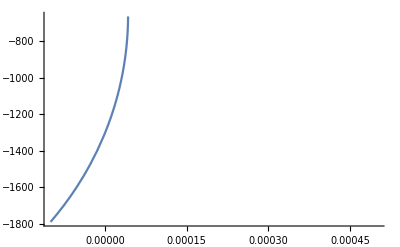

```mathematica
p1=Plot[L*Δkzsig[ws0,δsx,0,0],{δsx,-10^-4,5*10^-4}]
```

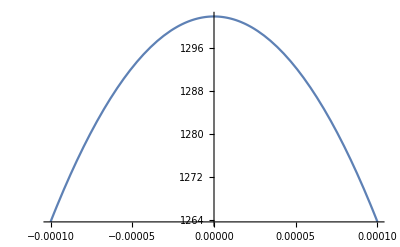

```mathematica
Plot[Abs[L*Δkzsig[ws0,0,δsy,0]],{δsy,-10^-4,10^-4}]
```

```mathematica
Plot[L*Δkzsig[ws,0,0,0],{ws,.9999*ws0,1.0002*ws0}]
```

-Graphics-

```mathematica
Plot[Abs[L*Δkzsig[ws,0,0,0]-L*Δkzsig[ws0,0,0,0]],{ws,.95*ws0,1.05*ws0}]
```

-Graphics-

## Nonlinearity

```mathematica
η=Sqrt[u0/ϵ0];
```

```mathematica
J=I*q*(n^2-1)*normstructurefactor*G*ϵ0* Cos[θi0+δix[ws,δsx,δp]]*Cos[2*θB]/(2*m*ws0)/.{n->nvisible[λv[wp0-ws]]};
```

```mathematica
deff=-I*J/(2*ϵ0*ws0)
```

(4.7318×10^-18+0. ⅈ) ((0.3306 (1.36719×10^19-ws)^2)/(-30625+(1.36719×10^19-ws)^2)+(4.3356 (1.36719×10^19-ws)^2)/(-11236+(1.36719×10^19-ws)^2)) Cos[0.730949+ArcSin[(299792458 (4.98249×10^10-4.56041×10^10 Sin[0.578278-δp]-(ws Sin[0.578288+δsx] (1-(2.80753×10^32 InterpolatingFunction[…][ws])/ws^2))/299792458))/(√(1+(1.17302×10^36)/((-30625+(359502071494727056000000000000000000 π^2)/((1.36719×10^19-ws)^2)) (1.36719×10^19-ws)^2)+(1.53833×10^37)/((-11236+(359502071494727056000000000000000000 π^2)/((1.36719×10^19-ws)^2)) (1.36719×10^19-ws)^2)) (1.36719×10^19-ws))]]

```mathematica
(*κ1[ws_,δsx_,δp_]=(2*hb*ws*(wp0-ws)*wp0/(c*ϵ0)^3/n^2)^0.5*ϵ0*deff/.{n->nvisible[λv[wp0-ws]]};*)
κ1[ws_,δsx_,δp_]=(2*hb*ws*(wp0-ws)*wp0/(c*ϵ0)^3/n)^0.5*ϵ0*deff/.{n->nvisible[λv[wp0-ws]]};
```

```mathematica
κsig[ws_,δsx_,δp_]:=If[Im[δix[ws,δsx,δp]]==0,κ1[ws,δsx,δp],0]
```

```mathematica
Abs[κsig[ws0,0,0]]^2
```

8.14009×10^-29

```mathematica
Plot[Abs[κsig[ws,0,0]]^2,{ws,0.9995*ws0,1.0005*ws0}]
```

-Graphics-

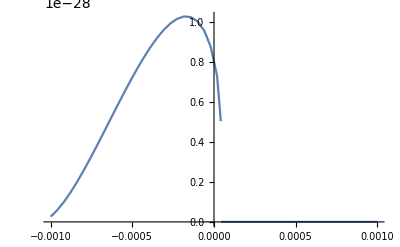

```mathematica
Plot[Abs[κsig[ws0,δsx,0]]^2,{δsx,-1*10^-3,1*10^-3}]
```

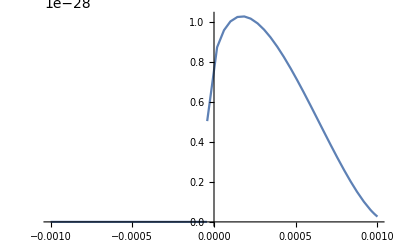

```mathematica
Plot[Abs[κsig[ws0,0,δp]]^2,{δp,-1*10^-3,1*10^-3}]
```

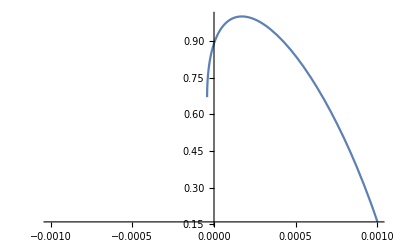

```mathematica
Plot[Cos[θi0+δix[ws0,0,δp]],{δp,-1*10^-3,1*10^-3}]
```

```mathematica
λv[wp0-0.9995*wp0]
```

275.551

```mathematica
λv[wp0-0.99989*wp0]
```

1252.5

```mathematica
r=1/(Sqrt[Abs[Cos[θs0]*Cos[θi0+δix[ws,δsx,δp]]]]);
```

```mathematica
κsig1=κsig[ws0,0,0]
```

9.02224×10^-15+0. ⅈ

## Formuli (from Laue Matrix 7)

### Signal

```mathematica
κsig[ws0]
```

κsig[1.36689×10^19]

```mathematica
signalintegrand[ws_,δsx_,δsy_,δp_]=-1*10^13*1/(2*Pi)^3*Cos[θs0]*ws^2/c^2*(4 r^2 Sin[1/2 L Δkzsig[ws,δsx,δsy,δp]]^2 κsig[ws,δsx,δp]^2)/Δkzsig[ws,δsx,δsy,δp]^2;
(*signalintegrand2theta[ws_,δsx_,δsy_]=-2*10^13*1/(2*Pi)^3*Cos[θs0]*ws^2/c^2*(4 r^2 Sin[1/2 L Δkzsig[ws,δsx,δsy,Δ]]^2 κsig[ws,δsx,Δ]^2)/Δkzsig[ws,δsx,δsy,Δ]^2;*)
```

```mathematica
Clear[signalintegrand,signalintegrand1,signalintegrand2]
```

### Signal

```mathematica
δp=0;
```

```mathematica
κsig[ws0,0,0]
```

9.02224×10^-15+0. ⅈ

```mathematica
(*signalintegrand[ws_,δsx_,δsy_,δ_]=10^13*1/(2*Pi)^3*Cos[θs0]*ws^2/c^2*16 Abs[(r Cos[1/2 (δ-L Δkzsig[ws,δsx,δsy,0])] Sin[1/2 L Δkzsig[ws,δsx,δsy,0]] κsig[ws,0,0])/Δkzsig[ws,δsx,δsy,0]]^2;*)
```

```mathematica
signalintegrand[ws_,δsx_,δsy_,δ_]=((10^13*1/(2*Pi)^3*Cos[θs0]*ws^2/c^2)*Abs[2*L^2*((I*r*κsig[ws0,0,0])^2)*(1+Cos[L*Δkzsig[ws,δsx,δsy,0]-2 δ])*Sinc[(L*Δkzsig[ws,δsx,δsy,0])/2]^2]);
```

```mathematica
signalintegrand1[ws_,δsx_,δsy_,δ_]:=If[Im[δix[ws,δsx,0]]==0,signalintegrand[ws,δsx,δsy,δ],0]
signalintegrand2[ws_,δsx_,δsy_,δ_]:=If[Im[δiy[ws,δsy]]==0,signalintegrand1[ws,δsx,δsy,δ],0]
```

```mathematica
signalintegrand2[ws0,0,0,0]
```

6.76316×10^-11

### Phase difference dependence

```mathematica
wlow=0.99991; whigh=1.00009;numbersteps=10;stepsize=(whigh-wlow)/numbersteps;
```

```mathematica
ϕsignalmax1x=θslim[0.1]
```

0.0000258499

```mathematica
ϕsignalmax1y=θslimy[0.1]
```

0.0000535642

```mathematica
ϕsignalmax1x*10^4
```

0.258499

```mathematica
Chop[NIntegrate[signalintegrand2[ws,δsx,δsy,0],{δsx,-1*0.00004,0.00004},{δsy,-1*0.00003,0.00003},{ws,wlow*ws0,whigh*ws0},Method->{"QuasiMonteCarlo","MaxPoints"->10^5}]]
```

0.000368051

```mathematica
phase[δ_]:=Chop[NIntegrate[signalintegrand2[ws,δsx,δsy,δ],{δsx,-1*0.00003,0.00003},{δsy,-1*0.00003,0.00003},{ws,wlow*ws0,whigh*ws0},Method->{"QuasiMonteCarlo","MaxPoints"->10^5}]]
```

```mathematica
phase[π/2]
```

0.000825807

```mathematica
Clear[phasedata]
phasedata=ParallelTable[{δ1,phase[δ1]},{δ1,-2*Pi,2*Pi,0.1*Pi}]
```

{{-6.28319,0.00027234},{-5.96903,0.000327855},{-5.65487,0.000467528},{-5.34071,0.000638442},{-5.02655,0.000775582},{-4.71239,0.000825807},{-4.39823,0.000770598},{-4.08407,0.000632238},{-3.76991,0.000461424},{-3.45575,0.000324829},{-3.14159,0.00027234},{-2.82743,0.000327855},{-2.51327,0.000467528},{-2.19911,0.000638442},{-1.88496,0.000775582},{-1.5708,0.000825807},{-1.25664,0.000770598},{-0.942478,0.000632238},{-0.628319,0.000461424},{-0.314159,0.000324829},{0.,0.00027234},{0.314159,0.000327855},{0.628319,0.000467528},{0.942478,0.000638442},{1.25664,0.000775582},{1.5708,0.000825807},{1.88496,0.000770598},{2.19911,0.000632238},{2.51327,0.000461424},{2.82743,0.000324829},{3.14159,0.00027234},{3.45575,0.000327855},{3.76991,0.000467528},{4.08407,0.000638442},{4.39823,0.000775582},{4.71239,0.000825807},{5.02655,0.000770598},{5.34071,0.000632238},{5.65487,0.000461424},{5.96903,0.000324829},{6.28319,0.00027234}}

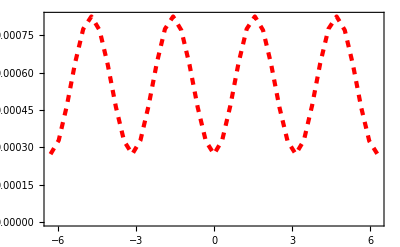

```mathematica
ListPlot[phasedata,Joined->True,PlotStyle->{{RGBColor[1,0,0],Dashed,AbsoluteThickness[3]}},Frame->True,BaseStyle->{FontWeight->"Bold",FontSize->18}]
```

```mathematica
visibility=(Max[Last/@Level[Cases[%,_Line,Infinity],{-2}]]-Min[Last/@Level[Cases[%,_Line,Infinity],{-2}]])/(Max[Last/@Level[Cases[%,_Line,Infinity],{-2}]]+Min[Last/@Level[Cases[%,_Line,Infinity],{-2}]])
```

0.504001

```mathematica
Clear[wlow,whigh]
wlow[Δrelative_]:=1-Δrelative;whigh[Δrelative_]:=1+Δrelative;
Eiwhigh[Δrelative_]:=(wp0-ws0*wlow[Δrelative])*(hb/q)
Eiwlow[Δrelative_]:=(wp0-ws0*whigh[Δrelative])*(hb/q)
ΔEi[Δrelative_]:=Eiwhigh[Δrelative]-Eiwlow[Δrelative]
```

```mathematica
Eiwhigh[Δrelative]
Eiwlow[Δrelative]
```

6.58284×10^-16 (1.36719×10^19-1.36689×10^19 (1-Δrelative))

6.58284×10^-16 (1.36719×10^19-1.36689×10^19 (1+Δrelative))

```mathematica
phaseΔrel[Δrelative_,δ_]:=Chop[NIntegrate[signalintegrand2[ws,δsx,δsy,δ],{δsx,-1*0.00003,0.00003},{δsy,-1*0.00003,0.00003},{ws,wlow[Δrelative]*ws0,whigh[Δrelative]*ws0},Method->{"QuasiMonteCarlo","MaxPoints"->10^5}]]
```

```mathematica
Clear[phaseΔrelDiscrt]
phaseΔrelDiscrt[Δrelative_]:=Table[phaseΔrel[Δrelative,δ],{δ,0,2*Pi,0.1*Pi}];
```

```mathematica
numberstepsΔEi=2;
ΔrelativeLow=0.00001;
ΔrelativeHigh=0.00009;
stepsizeΔEi=(ΔrelativeHigh-ΔrelativeLow)/numberstepsΔEi
```

0.00004

```mathematica
Clear[contrastDiscrt]
contrastDiscrt[Δrelative_]:=(Max[phaseΔrelDiscrt[Δrelative]]-Min[phaseΔrelDiscrt[Δrelative]])/(Max[phaseΔrelDiscrt[Δrelative]]+Min[phaseΔrelDiscrt[Δrelative]]);
```

```mathematica
Δrelative=0.05;
contrastDiscrt[Δrelative]
```

0.943877

```mathematica
Clear[dataVisVsΔEi]
dataVisVsΔEi=ParallelTable[{ΔEi[q2],contrastDiscrt[q2]},{q2,ΔrelativeLow,ΔrelativeHigh,stepsizeΔEi}];
```

```mathematica
ListPlot[dataVisVsΔEi,Joined->True,PlotStyle->{Thickness[0.008]},BaseStyle->{FontWeight->"Bold",FontSize->18}]
```

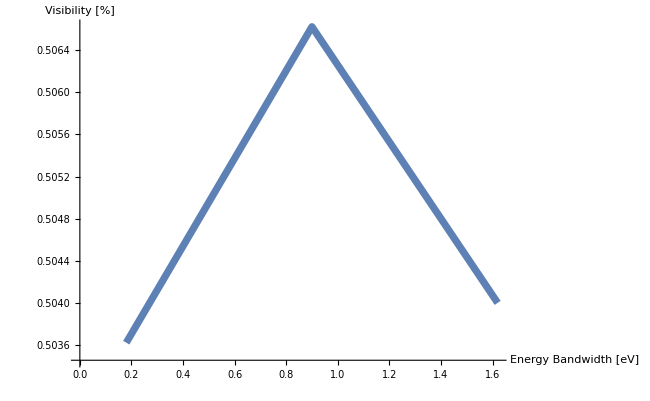

```mathematica
Show[%,AxesLabel->{HoldForm["Energy Bandwidth [eV]"],HoldForm["Visibility [%]"]},PlotLabel->None,LabelStyle->{18,GrayLevel[0]}]
```

```mathematica
numberstepsΔEs=20;
ΔrelativeSLow=0.005;
ΔrelativeSHigh=0.05;
stepsizeΔEs=(ΔrelativeSHigh-ΔrelativeSLow)/numberstepsΔEs
```

0.00225

```mathematica
Clear[dataVisVsΔEiSig]
dataVisVsΔEiSig=ParallelTable[{ΔEi[q3],contrastDiscrt[q3]},{q3,ΔrelativeSLow,ΔrelativeSHigh,stepsizeΔEs}];
```

```mathematica
ListPlot[dataVisVsΔEiSig,Joined->True,PlotStyle->{Thickness[0.008]},BaseStyle->{FontWeight->"Bold",FontSize->18}]
```

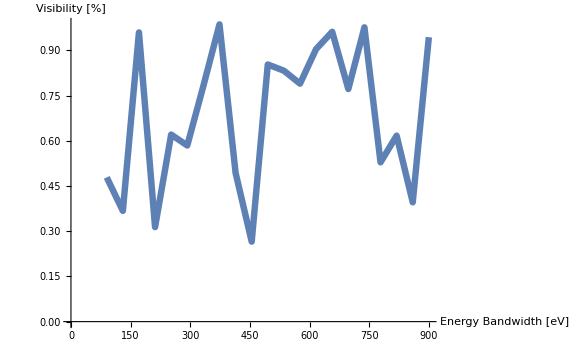

```mathematica
Show[%,AxesLabel->{HoldForm["Energy Bandwidth [eV]"],HoldForm["Visibility [%]"]},PlotLabel->None,LabelStyle->{18,GrayLevel[0]}]
```

```mathematica
phaseΔrel2[Δrelative_,δ_]:=Chop[NIntegrate[signalintegrand2[ws,δsx,0,δ],{ws,wlow[Δrelative]*ws0,whigh[Δrelative]*ws0},{δsx,-0.00004,0.00004},Method->{"QuasiMonteCarlo","MaxPoints"->10^5}]]
```

```mathematica
Clear[phaseΔrelDiscrt2]
phaseΔrelDiscrt2[Δrelative_]:=Table[phaseΔrel2[Δrelative,δ],{δ,0,2*Pi,0.1*Pi}];
```

```mathematica
numberstepsΔEi2=20;
ΔrelativeLow2=0.000000001;
ΔrelativeHigh2=0.00000003;
stepsizeΔEi2=(ΔrelativeHigh2-ΔrelativeLow2)/numberstepsΔEi2
```

1.45×10^-9

```mathematica
Clear[contrastDiscrt2]
contrastDiscrt2[Δrelative_]:=(Max[phaseΔrelDiscrt2[Δrelative]]-Min[phaseΔrelDiscrt2[Δrelative]])/(Max[phaseΔrelDiscrt2[Δrelative]]+Min[phaseΔrelDiscrt2[Δrelative]]);
```

```mathematica
Clear[dataVisVsΔEi2]
dataVisVsΔEi2=ParallelTable[{ΔEi[q2],contrastDiscrt2[q2]},{q2,ΔrelativeLow2,ΔrelativeHigh2,stepsizeΔEi2}];
```

```mathematica
ListPlot[dataVisVsΔEi2,Joined->True,PlotStyle->{Thickness[0.008]},BaseStyle->{FontWeight->"Bold",FontSize->18}]
```

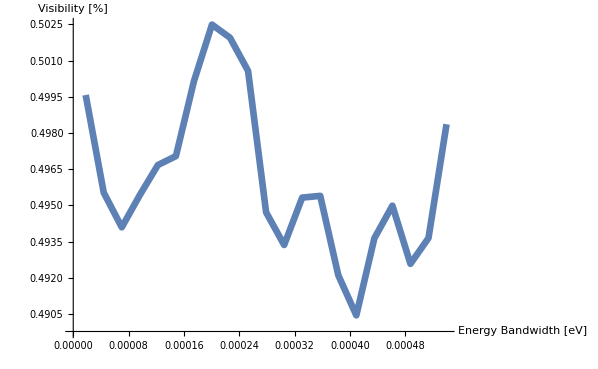

```mathematica
Show[%,AxesLabel->{HoldForm["Energy Bandwidth [eV]"],HoldForm["Visibility [%]"]},PlotLabel->None,LabelStyle->{18,GrayLevel[0]}]
```

# without integrating over δsx,δsy

```mathematica
phaseΔrel2[Δrelative_,δ_]:=Chop[NIntegrate[signalintegrand2[ws,0,0,δ],{ws,wlow[Δrelative]*ws0,whigh[Δrelative]*ws0},Method->{"QuasiMonteCarlo","MaxPoints"->10^5}]]
```

```mathematica
Clear[phaseΔrelDiscrt2]
phaseΔrelDiscrt2[Δrelative_]:=Table[phaseΔrel2[Δrelative,δ],{δ,0,2*Pi,0.1*Pi}];
```

```mathematica
numberstepsΔEi2=20;
ΔrelativeLow2=0.00001;
ΔrelativeHigh2=0.00009;
stepsizeΔEi2=(ΔrelativeHigh2-ΔrelativeLow2)/numberstepsΔEi2
```

4.×10^-6

```mathematica
Clear[contrastDiscrt2]
contrastDiscrt2[Δrelative_]:=(Max[phaseΔrelDiscrt2[Δrelative]]-Min[phaseΔrelDiscrt2[Δrelative]])/(Max[phaseΔrelDiscrt2[Δrelative]]+Min[phaseΔrelDiscrt2[Δrelative]]);
```

```mathematica
Clear[dataVisVsΔEi2]
dataVisVsΔEi2=ParallelTable[{ΔEi[q2],contrastDiscrt2[q2]},{q2,ΔrelativeLow2,ΔrelativeHigh2,stepsizeΔEi2}];
```

```mathematica
ListPlot[dataVisVsΔEi2,Joined->True,PlotStyle->{Thickness[0.008]},BaseStyle->{FontWeight->"Bold",FontSize->18}]
```

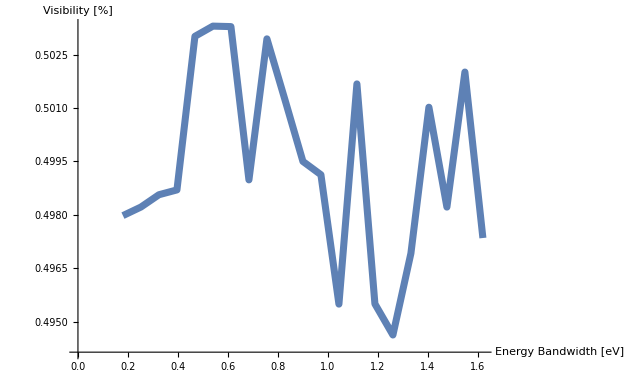

```mathematica
Show[%,AxesLabel->{HoldForm["Energy Bandwidth [eV]"],HoldForm["Visibility [%]"]},PlotLabel->None,LabelStyle->{18,GrayLevel[0]}]
```

# without integrating over δsx,δsy

```mathematica
phaseΔrel2[Δrelative_,δ_]:=Chop[NIntegrate[signalintegrand2[ws,0,0,δ],{ws,wlow[Δrelative]*ws0,whigh[Δrelative]*ws0},Method->{"QuasiMonteCarlo","MaxPoints"->10^5}]]
```

```mathematica
Clear[phaseΔrelDiscrt2]
phaseΔrelDiscrt2[Δrelative_]:=Table[phaseΔrel2[Δrelative,δ],{δ,0,2*Pi,0.1*Pi}];
```

```mathematica
numberstepsΔEi2=20;
ΔrelativeLow2=0.000000001;
ΔrelativeHigh2=0.000000019;
stepsizeΔEi2=(ΔrelativeHigh2-ΔrelativeLow2)/numberstepsΔEi2
```

9.×10^-10

```mathematica
Clear[contrastDiscrt2]
contrastDiscrt2[Δrelative_]:=(Max[phaseΔrelDiscrt2[Δrelative]]-Min[phaseΔrelDiscrt2[Δrelative]])/(Max[phaseΔrelDiscrt2[Δrelative]]+Min[phaseΔrelDiscrt2[Δrelative]]);
```

```mathematica
Clear[dataVisVsΔEi2]
dataVisVsΔEi2=ParallelTable[{ΔEi[q2],contrastDiscrt2[q2]},{q2,ΔrelativeLow2,ΔrelativeHigh2,stepsizeΔEi2}];
```

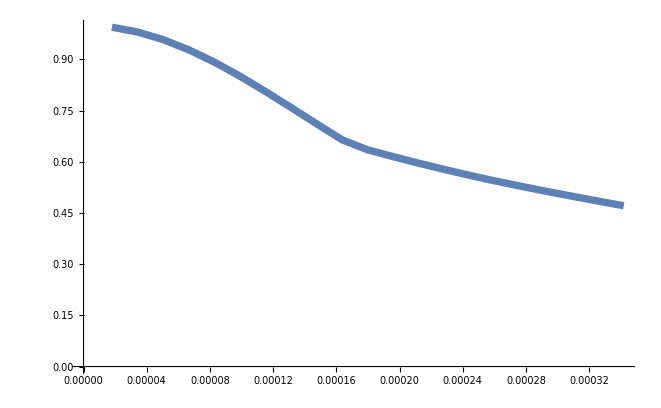

```mathematica
ListPlot[dataVisVsΔEi2,Joined->True,PlotStyle->{Thickness[0.008]},BaseStyle->{FontWeight->"Bold",FontSize->18}]
```

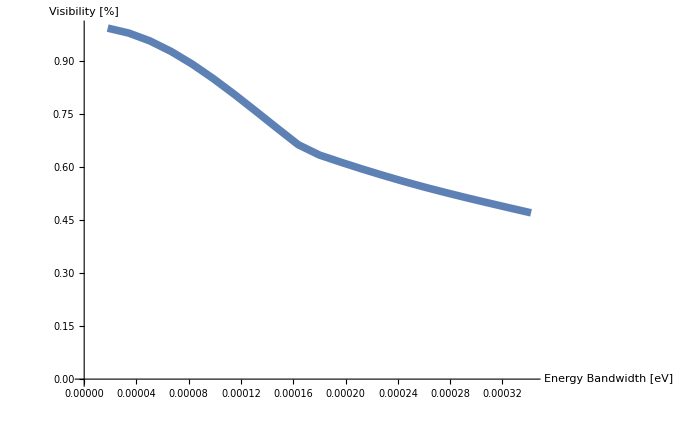

```mathematica
Show[%,AxesLabel->{HoldForm["Energy Bandwidth [eV]"],HoldForm["Visibility [%]"]},PlotLabel->None,LabelStyle->{18,GrayLevel[0]}]
```

# with Wp gaussian without integrating over δsx,δsy

```mathematica
(*signalintegrand[ws0,0,0,0]*)
```

```mathematica
signalintegrand1[ws_,δsx_,δsy_,δp_]:=If[Im[δix[ws,δsx,δp]]==0,signalintegrand[ws,δsx,δsy,δp],0]
signalintegrand2[ws_,δsx_,δsy_,δp_]:=If[Im[δiy[ws,δsy]]==0,signalintegrand1[ws,δsx,δsy,δp],0]
(*signalintegrand2theta1[ws_,δsx_,δsy_]:=If[Im[δix[ws,δsx]]==0,signalintegrand2theta[ws,δsx,δsy],0]
signalintegrand2theta2[ws_,δsx_,δsy_]:=If[Im[δiy[ws,δsy]]==0,signalintegrand2theta1[ws,δsx,δsy],0]*)
```

### Idler

```mathematica
idlerintegrand[ws_,δsx_,δsy_,δp_]=-1*10^13*1/(2*Pi)^3*Cos[θs0]*ws^2/c^2*(4 r^2 Sin[1/2 L Δkzsig[ws,δsx,δsy,δp]]^2 κsig[ws,δsx,δp]^2)/Δkzsig[ws,δsx,δsy,δp]^2;
```

```mathematica
idlerintegrand[ws0,0,0,0]
```

-1.6211×10^-10+0. ⅈ

```mathematica
idlerintegrand1[ws_,δsx_,δsy_,δp_]:=If[Im[δix[ws,δsx,δp]]==0,idlerintegrand[ws,δsx,δsy,δp],0]
idlerintegrand2[ws_,δsx_,δsy_,δp_]:=If[Im[δiy[ws,δsy]]==0,idlerintegrand1[ws,δsx,δsy,δp],0]
```

### Coincidence

```mathematica
coin1integrand[ws_,δsx_,δsy_,δp_]=1*10^13*1/(2*Pi)^3*Cos[θs0]*ws^2/c^2*Abs[((-1+ⅇ^(-ⅈ L Δkzsig[ws,δsx,δsy,δp])) r κsig[ws,δsx,δp])/Δkzsig[ws,δsx,δsy,δp]]^2;
```

```mathematica
coinintegrand1[ws_,δsx_,δsy_,δp_]:=If[Im[δix[ws,δsx,δp]]==0,coin1integrand[ws,δsx,δsy,δp],0]
coinintegrand2[ws_,δsx_,δsy_,δp_]:=If[Im[δiy[ws,δsy]]==0,coinintegrand1[ws,δsx,δsy,δp],0]
```

### Signal Integration

```mathematica
wlow=1-1.102*10^-4; whigh=1+1.102*10^-4;numbersteps=20;stepsize=(whigh-wlow)/numbersteps;
(*300mev @ 11keV -> 0.136e-4*)
```

```mathematica
(*δsxlow=-12.7119*10^-4; δsxhigh=12.7119*10^-4;*)
```

```mathematica
sig[ws_]:=Chop[NIntegrate[Chop[Abs[signalintegrand2[ws,δsx,δsy,0]],10^-10],{δsx,-5*10^-5,5*10^-5},{δsy,-3*10^-4,3*10^-4},Method->{"QuasiMonteCarlo","MaxPoints"->10^4}],10^-19];
```

```mathematica
signalintegrand2[ws0,0,0,0]
```

-6.28456×10^-11+0. ⅈ

```mathematica
Plot3D[Abs[signalintegrand2[ws0,δsx,δsy,0]],{δsx,-0.012,0.012},{δsy,-0.03,0.03}]
```

-Graphics3D-

```mathematica
data1=Table[{(1-q1)*ws0*hb/q,sig[q1*ws0]},{q1,wlow,whigh,stepsize}];
```

NIntegrate::maxp: The integral failed to converge after 5417 integrand evaluations. NIntegrate obtained 2.86252×10^-18 and 2.8662×10^-20 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 10000 integrand evaluations. NIntegrate obtained 3.45712×10^-18 and 3.4775×10^-20 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 5400 integrand evaluations. NIntegrate obtained 3.96175×10^-18 and 3.97317×10^-20 for the integral and error estimates.

General::stop: Further output of NIntegrate :: maxp will be suppressed during this calculation.

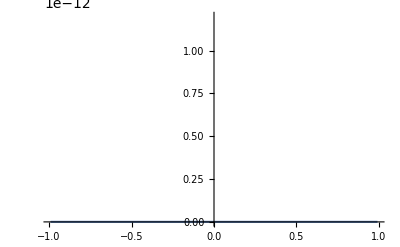

```mathematica
ListPlot[data1,Joined->True,PlotRange->{0,1.2*10^-12}]
```

```mathematica
traprule=ws0*stepsize*(Plus@@Transpose[data1][[2]]-(sig[wlow*ws0]+sig[whigh*ws0])/2)
```

NIntegrate::maxp: The integral failed to converge after 5417 integrand evaluations. NIntegrate obtained 2.86252×10^-18 and 2.8662×10^-20 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 6828 integrand evaluations. NIntegrate obtained 0. and 0. for the integral and error estimates.

0.00744913

```mathematica
check=Chop[NIntegrate[Abs[signalintegrand2[ws,δsx,δsy,0]],{δsx,-.0001,.0001},{δsy,-.003,.003},{ws,wlow*ws0,whigh*ws0},Method->{"QuasiMonteCarlo","MaxPoints"->10^3}]]
```

NIntegrate::maxp: The integral failed to converge after 1000 integrand evaluations. NIntegrate obtained 0.243863 and 0.0731847 for the integral and error estimates.

0.243863

```mathematica
Rocking curve
```

```mathematica
(*sigrock[δ_]:=Chop[NIntegrate[Chop[Abs[signalintegrand2[ws,δsx,δsy,δ]],10^-10],{δsx,-1*10^-4,1*10^-4},{δsy,-3*10^-4,3*10^-4},{ws,wlow*ws0,whigh*ws0},Method->{"QuasiMonteCarlo","MaxPoints"->10^5}],10^-19];*)
δlow=-10^-3; δhigh=1*10^-3; δres=1*10^-4;
(*δsxlow=-12.7119*10^-4; δsxhigh=12.7119*10^-4;*) (*1.5mm*)
(*δsxlow=-20*10^-4; δsxhigh=20*10^-4;*) (*4mm*)
(*δsxlow=-5*10^-4; δsxhigh=5*10^-4;*) (*1mm*)
δsxlow=-5*10^-3; δsxhigh=5*10^-3; (*0.1 mm at 615mm distance=0.1626mrad*)
(*δsxlow=-6.25*10^-4; δsxhigh=6.25*10^-4;*) (*2.5mm*)
(*δsxlow=-14.8305*10^-4; δsxhigh=14.8305*10^-4;*) (*1.75mm*)
δsylow=-5*10^-3; δsyhigh=5*10^-3; (*2 mm RS2*)
(*δsylow=-42.37*10^-4; δsyhigh=42.37*10^-4;*)(*δsylow=-42.37*10^-4δsyhigh=42.37*10^-4*)
sigrock[δ_]:=Chop[NIntegrate[Chop[Abs[signalintegrand2[ws,δsx,δsy,δ]],10^-10],{δsx,δsxlow,δsxhigh},{δsy,δsylow,δsyhigh},{ws,wlow*ws0,whigh*ws0},Method->{"QuasiMonteCarlo","MaxPoints"->1*10^4}],10^-19];
(* Integration over detector plase (angle) δsx(2theta direction) and δsy *)
```

```mathematica
(*datasigrock1=ParallelTable[{q1*10^4,sigrock[q1]},{q1,-1*10^-3,1*10^-3,2*10^-4}];*)
(*labmda_idler 600nm - {δsx,-4.2373*10^-4,4.2373*10^-4} (Detector effective aperture - RS2 hor. in radians),{δsy,-2.1186*10^-4,2.1186*10^-4} (RS1 aperture (min of RS1 and RS2 ver.) in radians)*)

datasigrock1=ParallelTable[{q1(**10^3*),sigrock[q1]},{q1,δlow,δhigh,δres}]; (* The last value is the rocking curve resolution*)
```

NIntegrate::maxp: The integral failed to converge after 6828 integrand evaluations. NIntegrate obtained 0.015936 and 0.00227927 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 6828 integrand evaluations. NIntegrate obtained 0.0496413 and 0.009594 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 6828 integrand evaluations. NIntegrate obtained 1.20679 and 0.575765 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 6828 integrand evaluations. NIntegrate obtained 0.0146236 and 0.00209692 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 6828 integrand evaluations. NIntegrate obtained 0.0277775 and 0.00409453 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 6828 integrand evaluations. NIntegrate obtained 0.0800557 and 0.0118511 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 6828 integrand evaluations. NIntegrate obtained 3.59941 and 2.84818 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 6828 integrand evaluations. NIntegrate obtained 2539.1 and 2476.43 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 6828 integrand evaluations. NIntegrate obtained 0.0160274 and 0.00215251 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 6828 integrand evaluations. NIntegrate obtained 0.0359279 and 0.00603368 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 6828 integrand evaluations. NIntegrate obtained 0.0661359 and 0.0111974 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 6828 integrand evaluations. NIntegrate obtained 0.021776 and 0.00310323 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 6828 integrand evaluations. NIntegrate obtained 0.178782 and 0.039763 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 6828 integrand evaluations. NIntegrate obtained 94.2547 and 62.3727 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 6828 integrand evaluations. NIntegrate obtained 2366.1 and 2306.14 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 6828 integrand evaluations. NIntegrate obtained 65.9084 and 28.6476 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 6828 integrand evaluations. NIntegrate obtained 1.08146 and 0.275557 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 6828 integrand evaluations. NIntegrate obtained 0.138746 and 0.0204871 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 6828 integrand evaluations. NIntegrate obtained 0.29169 and 0.0516586 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 6828 integrand evaluations. NIntegrate obtained 0.0526412 and 0.00733164 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 6828 integrand evaluations. NIntegrate obtained 0.0891071 and 0.0128794 for the integral and error estimates.

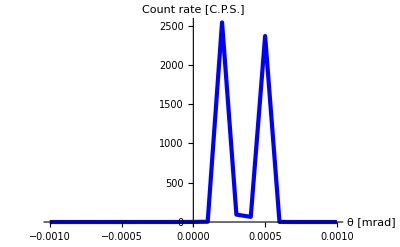

```mathematica
ListPlot[datasigrock1,Joined->True,LabelStyle->{FontFamily->"Times",FontSize->14,FontWeight->"Bold"},PlotStyle->{{RGBColor[0,0,1],AbsoluteThickness[3]}},AxesLabel->{Style["θ [mrad]",14,Black,Bold],Style["Count rate [C.P.S.]",14,Black,Bold]},PlotRange->All]
```

```mathematica
ΔkzSig[ws_,δsx_,δsy_,δp_]=wp0*n[wp0]*Cos[θp0+δp]/c-ws*n[ws]*Cos[θs0+δsx]*Cos[δsy]/c-(wp0-ws)*nvisible[wp0-ws]*Cos[θi0+δθi[ws,δsx,δp]]*Cos[δiy[ws,δsy]]/c;
```

```mathematica
SignalIntegrand[wi_,δsx_,δsy_]=((10^13*1/(2*Pi)^3*Cos[θi0]*wi^2/c^2)*Abs[2*L^2*((I*r*κsig[ws0,0,0])^2)*Sinc[(L*Δkzsig[wp0-wi,δsx,δsy,0])/2]^2]);
```

```mathematica
SignalIntegrand1[wi_,δsx_,δsy_]:=If[Im[δix[wp0-wi,δsx,0]]==0,SignalIntegrand[wi,δsx,δsy],0]
SignalIntegrand2[wi_,δsx_,δsy_]:=If[Im[δiy[wp0-wi,δsy]]==0,SignalIntegrand1[wi,δsx,δsy],0]
(*signalintegrand2theta1[ws_,δsx_,δsy_]:=If[Im[δix[ws,δsx]]==0,signalintegrand2theta[ws,δsx,δsy],0]
signalintegrand2theta2[ws_,δsx_,δsy_]:=If[Im[δiy[ws,δsy]]==0,signalintegrand2theta1[ws,δsx,δsy],0]*)
```

```mathematica
datasigRock[δsx_,δsy_]:=Chop[NIntegrate[Chop[Abs[SignalIntegrand2[wi,δsx,δsy]],10^-10],{wi,(1-0.3)*wi0,(1+0.3)*wi0},Method->{"QuasiMonteCarlo","MaxPoints"->1*10^4}],10^-19];
```

```mathematica
DensityPlot[datasigRock[δsx,δsy],{δsx,-10^-4,10^-4},{δsy,-10^-4,10^-4}]
```

NIntegrate::maxp: The integral failed to converge after 6828 integrand evaluations. NIntegrate obtained 0. and 0. for the integral and error estimates.

$Aborted

```mathematica
(*sigrock[δ_]:=Chop[NIntegrate[Chop[Abs[signalintegrand2[ws,δsx,δsy,δ]],10^-10],{δsx,-1*10^-4,1*10^-4},{δsy,-3*10^-4,3*10^-4},{ws,wlow*ws0,whigh*ws0},Method->{"QuasiMonteCarlo","MaxPoints"->10^5}],10^-19];*)
δlow=-10^-3; δhigh=1*10^-3; δres=1*10^-4;
(*δsxlow=-12.7119*10^-4; δsxhigh=12.7119*10^-4;*) (*1.5mm*)
(*δsxlow=-20*10^-4; δsxhigh=20*10^-4;*) (*4mm*)
(*δsxlow=-5*10^-4; δsxhigh=5*10^-4;*) (*1mm*)
δsxlow=-5*10^-3; δsxhigh=5*10^-3; (*0.1 mm at 615mm distance=0.1626mrad*)
(*δsxlow=-6.25*10^-4; δsxhigh=6.25*10^-4;*) (*2.5mm*)
(*δsxlow=-14.8305*10^-4; δsxhigh=14.8305*10^-4;*) (*1.75mm*)
δsylow=-5*10^-3; δsyhigh=5*10^-3; (*2 mm RS2*)
(*δsylow=-42.37*10^-4; δsyhigh=42.37*10^-4;*)(*δsylow=-42.37*10^-4δsyhigh=42.37*10^-4*)
sigRock[δ_]:=Chop[NIntegrate[Chop[Abs[signalintegrand2[ws,δsx,δsy,δ]],10^-10],{δsx,δsxlow,δsxhigh},{δsy,δsylow,δsyhigh},{ws,wlow*ws0,whigh*ws0},Method->{"QuasiMonteCarlo","MaxPoints"->1*10^4}],10^-19];
(* Integration over detector plase (angle) δsx(2theta direction) and δsy *)
```